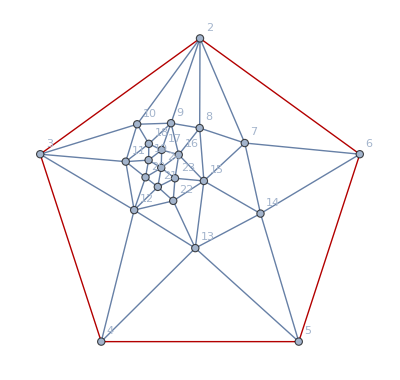

```mathematica
baseg =Graph[VertexDelete[ Graph[plantri[[10000]]],1],GraphHighlight->{2<->6,6<->5,5<->4,4<->3,3<->2}, GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
EmbedGraph[key_]:=Block[{val=newAssoc[key], sets, reference={2,6,5,4,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->4,4<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Monitor[Table[{key,If[
PlanarGraphQ[EmbedGraph[key]],
newAssoc[key]["comp"]=Greater,
newAssoc[key]["comp"]=GreaterEqual
]},{key,Keys[newAssoc]}],key]; Print["OK"]
```

OK

#### b11 - b15 are strictly bigger

```mathematica
Table[newAssoc[key]["comp"]=Greater,{key,{2190,84,6642,6588,2214}}]
```

{Greater,Greater,Greater,Greater,Greater}

#### b41 tot b45

```mathematica
Table[newAssoc[key]["comp"]=Greater,{key,{6670,8784,2460,21954,7374}}]
```

{Greater,Greater,Greater,Greater,Greater}

#### b46 tot b50

```mathematica
Table[newAssoc[key]["comp"]=Greater,{key,{9490,364,28764,27246,22708}}]
```

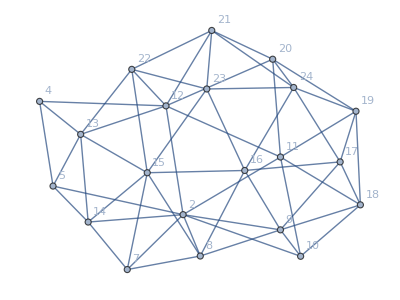

```mathematica
Graph[EmbedGraph[47694],VertexLabels->"Name"]
```

```mathematica
computed=Association[]
```

<||>

```mathematica
Monitor[Table[computed[key]=ChromaticPolynomial[EmbedGraph[key],4]/24,{key,Select[Keys[newAssoc],MemberQ[myVars,newAssoc[#]["colofour"]]&]}],key]
```

{3728,2520,3000,2488,1280,2852,1940,2852,2324,1292,2348,1590,1268,1108,264,2384,1596,1848,1500,712,2616,2120,1996,1682,894,1112,702,2640,1772,2038,2050,912,1112,870,976,746,224,2360,1558,1924,1598,796,980,672,1060,870,230,980,628,186,182}

```mathematica
abcdefg=Table[newAssoc[key]["colofour"]->computed[key],
{key,Select[Keys[newAssoc],MemberQ[myVars,newAssoc[#]["colofour"]]&]}]
```

{z→3728,b06→2520,b04→3000,b07→2488,b34→1280,b02→2852,b17→1940,b05→2852,b12→2324,b26→1292,b08→2348,b22→1590,b28→1268,b35→1108,b47→264,b10→2384,b21→1596,b20→1848,b24→1500,b40→712,b03→2616,b11→2120,b15→1996,b18→1682,b43→894,b33→1112,b38→702,b01→2640,b16→1772,b14→2038,b13→2050,b41→912,b30→1112,b45→870,b27→976,b42→746,b46→224,b09→2360,b25→1558,b19→1924,b23→1598,b39→796,b32→980,b37→672,b29→1060,b44→870,b50→230,b31→980,b36→628,b49→186,b48→182}

```mathematica
Grid[Sort[Table[{key,newAssoc[key]["colofour"],computed[key],Symbol["x"<>ToString[key]]/.graphics},{key,Select[Keys[newAssoc],MemberQ[myVars,newAssoc[#]["colofour"]]&]}],#1[[3]]>#2[[3]]&],Frame->All,Alignment->{Center,Center},ItemSize->10]
```

0 | z | 3728 | -Graphics-
3 | b04 | 3000 | -Graphics-
81 | b05 | 2852 | -Graphics-
27 | b02 | 2852 | -Graphics-
6561 | b01 | 2640 | -Graphics-
2187 | b03 | 2616 | -Graphics-
1 | b06 | 2520 | -Graphics-
9 | b07 | 2488 | -Graphics-
729 | b10 | 2384 | -Graphics-
19683 | b09 | 2360 | -Graphics-
243 | b08 | 2348 | -Graphics-
84 | b12 | 2324 | -Graphics-
2190 | b11 | 2120 | -Graphics-
6642 | b13 | 2050 | -Graphics-
6588 | b14 | 2038 | -Graphics-
2214 | b15 | 1996 | -Graphics-
36 | b17 | 1940 | -Graphics-
19686 | b19 | 1924 | -Graphics-
810 | b20 | 1848 | -Graphics-
6562 | b16 | 1772 | -Graphics-
2430 | b18 | 1682 | -Graphics-
19692 | b23 | 1598 | -Graphics-
738 | b21 | 1596 | -Graphics-
244 | b22 | 1590 | -Graphics-
19684 | b25 | 1558 | -Graphics-
972 | b24 | 1500 | -Graphics-
109 | b26 | 1292 | -Graphics-
13 | b34 | 1280 | -Graphics-
273 | b28 | 1268 | -Graphics-
7293 | b30 | 1112 | -Graphics-
2917 | b33 | 1112 | -Graphics-
333 | b35 | 1108 | -Graphics-
21951 | b29 | 1060 | -Graphics-
26487 | b31 | 980 | -Graphics-
20439 | b32 | 980 | -Graphics-
8757 | b27 | 976 | -Graphics-
6670 | b41 | 912 | -Graphics-
2460 | b43 | 894 | -Graphics-
21954 | b44 | 870 | -Graphics-
7374 | b45 | 870 | -Graphics-
19696 | b39 | 796 | -Graphics-
8784 | b42 | 746 | -Graphics-
1062 | b40 | 712 | -Graphics-
3160 | b38 | 702 | -Graphics-
20448 | b37 | 672 | -Graphics-
26488 | b36 | 628 | -Graphics-
364 | b47 | 264 | -Graphics-
22708 | b50 | 230 | -Graphics-
9490 | b46 | 224 | -Graphics-
27246 | b49 | 186 | -Graphics-
28764 | b48 | 182 | -Graphics-

```mathematica
Sort[Table[newAssoc[20665]["colofour"][[t]],{t,Length[newAssoc[20665]["colofour"]]}]]
```

{b11/6,b12/6,b13/6,b14/6,b15/6,-b16/3,-b17/3,-b18/3,-b19/3,-b20/3,b21/6,b22/6,b23/6,b24/6,b25/6,b36/3,b37/3,b38/3,b39/3,b40/3,-b41/6,-b42/6,-b43/6,-b44/6,-b45/6}

```mathematica
Table[newAssoc[20665]["colofour"][[t]],{t,Length[newAssoc[20665]["colofour"]]}]/.abcdefg
```

{1060/3,1162/3,1025/3,1019/3,998/3,-1772/3,-1940/3,-1682/3,-1924/3,-616,266,265,799/3,250,779/3,628/3,224,234,796/3,712/3,-152,-373/3,-149,-145,-145}

```mathematica
newAssoc[20665]["colofour"]//FullSimplify
```

1/6 (b11+b12+b13+b14+b15-2 b16-2 b17-2 b18-2 b19-2 b20+b21+b22+b23+b24+b25+2 b36+2 b37+2 b38+2 b39+2 b40-b41-b42-b43-b44-b45)

```mathematica
ChromaticPolynomial[VertexDelete[ Graph[plantri[[10000]]],1],4]/24
```

461

```mathematica
newAssoc[20665]["colofour"]/.abcdefg
```

461

```mathematica
Style[newAssoc[20665]["colofour"]/.graphics//FullSimplify,{Red,Bold}]
```

1/6 (-Graphics--2 -Graphics-+-Graphics-+-Graphics-+-Graphics--2 -Graphics--2 -Graphics-+-Graphics-+-Graphics-+-Graphics--2 -Graphics-+-Graphics-+-Graphics-+-Graphics--2 -Graphics-+2 -Graphics---Graphics-+2 -Graphics-+2 -Graphics---Graphics---Graphics---Graphics-+2 -Graphics---Graphics-+2 -Graphics-)

```mathematica
CosyPrint2[20665]
```

-Graphics-   -Graphics-   x20665+x46936==x982
x20665==x27226+x35977
x20665==x22852+x31681
x19936==x20665+x23608
x20422==x20665+x27550
x20665==x20746+x23041
x20665==x20692+x20803
x20656==x20665+x20758
x20665==x20668+x27259
x20664==x20665+x22856   (2 | 1 | 0 | 0 | 1
1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 1 | 2){20665→b11/6+b12/6+b13/6+b14/6+b15/6-b16/3-b17/3-b18/3-b19/3-b20/3+b21/6+b22/6+b23/6+b24/6+b25/6+b36/3+b37/3+b38/3+b39/3+b40/3-b41/6-b42/6-b43/6-b44/6-b45/6>0,}

```mathematica
1596/6
```

266

## Verification of the values and the formulas

#### Here the various x values correspond to alfa1, beta1, ... epsilon1. We can now use them to calculate the value of the wheelgraph. We present the vale, the formula and the graphic formula.

```mathematica
(x36166+x31738+x29608+x36112+x31714)/.replaceMents/.abcdefg
```

239

```mathematica
ChromaticPolynomial[Graph[plantri[[10000]]],4]/24
```

239

```mathematica
Style[FullSimplify[(x36166+x31738+x29608+x36112+x31714)/.replaceMents/.graphics],{Red,Bold}]
```

1/12 (-6 -Graphics-+6 -Graphics-+6 -Graphics--6 -Graphics--6 -Graphics-+6 -Graphics-+6 -Graphics--6 -Graphics-+6 -Graphics--6 -Graphics-+8 -Graphics--4 -Graphics-+8 -Graphics--4 -Graphics--4 -Graphics--4 -Graphics--4 -Graphics--4 -Graphics--4 -Graphics-+8 -Graphics--4 -Graphics-+8 -Graphics-+8 -Graphics--4 -Graphics--4 -Graphics-+6 -Graphics--6 -Graphics-+6 -Graphics--6 -Graphics--6 -Graphics-+6 -Graphics-+6 -Graphics--6 -Graphics--6 -Graphics-+6 -Graphics--5 -Graphics-+7 -Graphics--5 -Graphics--5 -Graphics-+7 -Graphics-+7 -Graphics-+7 -Graphics--5 -Graphics-+7 -Graphics--5 -Graphics--3 (-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-))

```mathematica
(x36166+x31738+x29608+x36112+x31714)/.replaceMents//Simplify
```

1/12 (6 b01+6 b02+6 b03+6 b04+6 b05-6 b06-6 b07-6 b08-6 b09-6 b10-4 b11-4 b12-4 b13-4 b14-4 b15-4 b16-4 b17-4 b18-4 b19-4 b20+8 b21+8 b22+8 b23+8 b24+8 b25-6 b26-6 b27-6 b28-6 b29-6 b30+6 b31+6 b32+6 b33+6 b34+6 b35-5 b36-5 b37-5 b38-5 b39-5 b40+7 b41+7 b42+7 b43+7 b44+7 b45-3 b46-3 b47-3 b48-3 b49-3 b50)

## Playing with cycle and wheel

```mathematica
(x36166+x31738+x29608+x36112+x31714)/.replaceMents
```

b01/2+b02/2+b03/2+b04/2+b05/2-b06/2-b07/2-b08/2-b09/2-b10/2-b11/3-b12/3-b13/3-b14/3-b15/3-b16/3-b17/3-b18/3-b19/3-b20/3+(2 b21)/3+(2 b22)/3+(2 b23)/3+(2 b24)/3+(2 b25)/3-b26/2-b27/2-b28/2-b29/2-b30/2+b31/2+b32/2+b33/2+b34/2+b35/2-(5 b36)/12-(5 b37)/12-(5 b38)/12-(5 b39)/12-(5 b40)/12+(7 b41)/12+(7 b42)/12+(7 b43)/12+(7 b44)/12+(7 b45)/12-b46/4-b47/4-b48/4-b49/4-b50/4

```mathematica
(-b46/4-b47/4-b48/4-b49/4-b50/4)/.abcdefg//N
```

-271.5

```mathematica
(newAssoc[20665]["colofour"]-((x36166+x31738+x29608+x36112+x31714)/.replaceMents)//FullSimplify)
```

1/4 (-2 b01-2 b02-2 b03-2 b04-2 b05+2 b06+2 b07+2 b08+2 b09+2 b10+2 b11+2 b12+2 b13+2 b14+2 b15-2 b21-2 b22-2 b23-2 b24-2 b25+2 b26+2 b27+2 b28+2 b29+2 b30-2 b31-2 b32-2 b33-2 b34-2 b35+3 b36+3 b37+3 b38+3 b39+3 b40-3 b41-3 b42-3 b43-3 b44-3 b45+b46+b47+b48+b49+b50)

```mathematica
(b01/2+b02/2+b03/2+b04/2+b05/2-b06/2-b07/2-b06/2-b07/2-b08/2-b09/2-b10/2-b11/3-b12/3-b13/3-b14/3-b15/3-b16/3-b17/3-b18/3-b19/3-b20/3)/.abcdefg//N
```

-8138.67

```mathematica
((+(2 b21)/3+(2 b22)/3+(2 b23)/3+(2 b24)/3+(2 b25)/3-b26/2-b27/2-b28/2-b29/2-b30/2+b31/2+b32/2+b33/2+b34/2+b35/2-(5 b36)/12-(5 b37)/12-(5 b38)/12-(5 b39)/12-(5 b40)/12+(7 b41)/12+(7 b42)/12+(7 b43)/12+(7 b44)/12+(7 b45)/12-b46/4-b47/4-b48/4-b49/4-b50/4))/.abcdefg//N
```

5873.67

```mathematica
((newAssoc[20665]["colofour"]-((x36166+x31738+x29608+x36112+x31714)/.replaceMents)//FullSimplify))/2//getAllVariables//Length
```

45

```mathematica
CosyPrint2[36166]
```

-Graphics-   -Graphics-   x35434==x36166+x36898
x36138==x36166+x36194
x14044==x36166+x58288   (2 | 1 | 2 | 1 | 1
1 | 2 | 1 | 2 | 1
2 | 1 | 2 | 1 | 1
1 | 2 | 1 | 2 | 1
1 | 1 | 1 | 1 | 2){36166→b01/3-b03/6+b05/3-b07/6-b08/6-b09/6+b11/6-b12/3-b14/3+b15/6-b16/3+b17/6+b19/6-b20/3+b21/6+b22/6+b24/6+b25/6-b26/3+b28/6-b30/3+b32/6+b33/6+b34/6-b36/12-b37/12-b38/12-b39/12-b40/12+(5 b41)/12-b42/12-b43/12-b44/12+(5 b45)/12-b46/12-b47/12+b48/12-b49/12-b50/12≥0,}